# Proyecto Genérico

Curso: Sistemas Dinámicos
Catedrático: Lic. José Bonilla
Alumno: Diego Sarceño - 201900109

```mathematica
box[{x_,y_},{X_,Y_}]:=Line[{{x,y},{x,Y},{X,Y},{X,y},{x,y}}];
```

## Problema 1.3:

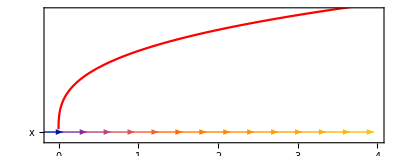

```mathematica
(* a) Diagrama de Fase de: f(x)=x^(1/3) *)
vectF=VectorPlot[{x^(1/3),0},{x,-0.1,4},{y,-0.1,1.5},AspectRatio->Automatic,FrameTicks->{Automatic,{{0,"x"}}},VectorPoints->Table[{value,0},{value,-0.1,4,0.3}]];
xF=Plot[x^(1/3),{x,-0.1,4},PlotStyle->Red];
Show[vectF,xF]
```

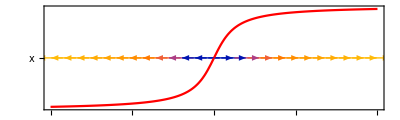

```mathematica
(* b) Diagrama de Fase de: f(x)=2*ArcTan[x] *)
vectArc=VectorPlot[{2*ArcTan[x],0},{x,-10,10},{y,-3,3},AspectRatio->Automatic,FrameTicks->{Automatic,{{0,"x"}}},VectorPoints->Table[{value,0},{value,-10,10,0.8}]];
arcTan=Plot[2*ArcTan[x],{x,-10,10},PlotStyle->Red];
Show[vectArc,arcTan]
```

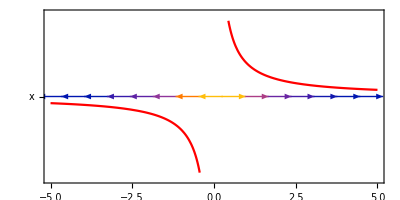

```mathematica
(* c) Diagrama de Fase de: f(x)=1/x *)
vectInv=VectorPlot[{1/x,0},{x,-5,5},{y,-2.5,2.5},AspectRatio->Automatic,FrameTicks->{Automatic,{{0,"x"}}},VectorPoints->Table[{value,0},{value,-5,5,0.7}]];
xInv=Plot[1/x,{x,-5,5},PlotStyle->Red];
Show[vectInv,xInv]
```

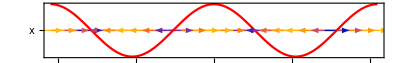

```mathematica
(* d) Diagrama de Fase de: f(x)=Cos[x] *)
vectCOS=VectorPlot[{Cos[x],0},{x,-2*π,2*π},{y,-1,1},AspectRatio->Automatic,FrameTicks->{Automatic,{{0,"x"}}},VectorPoints->Table[{value,0},{value,-2*π,2*π,0.5}]];
cos=Plot[Cos[x],{x,-2*π,2*π},PlotStyle->Red];
Show[vectCOS,cos]
```

## Problema 2.1

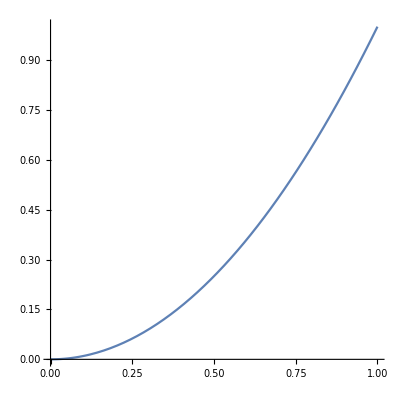

```mathematica
Plot[x^2,{x,0,1},AspectRatio->1]
```

## Problema 4.3

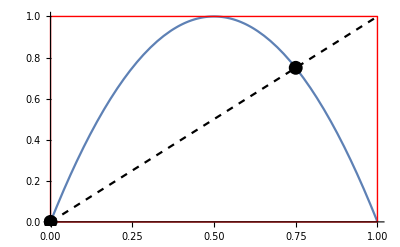

```mathematica
cuadratic=Plot[4*x*(1-x),{x,0,1}];
caja=Graphics[{Red,Thick,box[{0,0},{1,1}]},AspectRatio->Automatic];
slope=Plot[x,{x,0,1},PlotStyle->{Black,Dashed}];
solutions=Graphics[{PointSize[0.025],Point[{{0,0},{3/4,3/4}},VertexColors->{Green, Green}]}];


Show[cuadratic,caja,slope,solutions]
```

```mathematica
Solve[{4*y*(1-y)==y},y]
```

{{y→0},{y→3/4}}

## Problema 4.5

```mathematica
Solve[{3.2*p*(1-p)==p},p]
```

{{p→0.},{p→0.6875}}

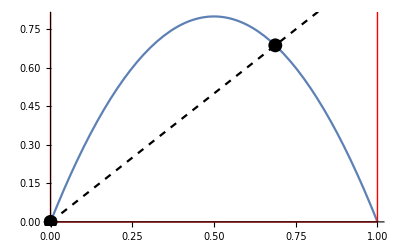

```mathematica
cuadratic45=Plot[3.2*x*(1-x),{x,0,1}];
caja45=Graphics[{Red,Thick,box[{0,0},{1,0.84}]},AspectRatio->Automatic];
slope45=Plot[x,{x,0,1},PlotStyle->{Black,Dashed}];
solutions45=Graphics[{PointSize[0.025],Point[{{0,0},{0.6875,0.6875}},VertexColors->{Green, Green}]}];


Show[cuadratic45,caja45,slope45,solutions45]
```

## Problema 4.10

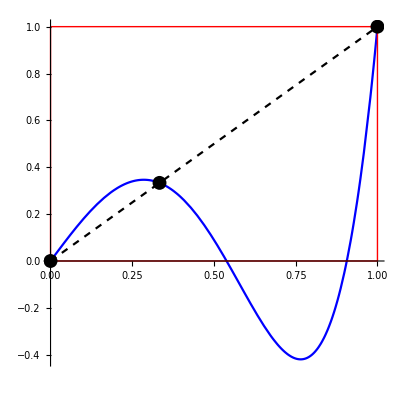

```mathematica
(* Tomaremos el polinomio de Legendre restringido al intervalo [0,1] *)
pleg=Plot[LegendreP[5,x],{x,0,1},AspectRatio->1,PlotStyle->Blue];
caja410=Graphics[{Red,Thick,box[{0,0},{1,1}]},AspectRatio->-1];
solutions410=Graphics[{PointSize[0.025],Point[{{0,0},{1/3,1/3},{1,1}},VertexColors->{Green, Green,Green}]}];

Show[pleg,slope,caja410,solutions410]
```

```mathematica
Solve[{LegendreP[5,t]==t},t]
```

{{t→-1},{t→-1/3},{t→0},{t→1/3},{t→1}}

## Problema 6.1

```mathematica
(* a) f(x)=-x^3 *)
```

```mathematica
x=.;
Solve[{-x^3==x},x]
```

{{x→0},{x→-ⅈ},{x→ⅈ}}

```mathematica
D[-x^3-x,x]
```

-1-3 x^2

```mathematica
(* b) p(x)=x^3-x *)
```

```mathematica
x=.;
Solve[{x^3-x==x},x]
```

{{x→0},{x→-√2},{x→√2}}

```mathematica
D[x^3-2*x,x]
```

-2+3 x^2

```mathematica
(* c) f(x)=-x^3-x *)
```

```mathematica
x=.;
Solve[{-x^3-x==x},x]
```

{{x→0},{x→-ⅈ √2},{x→ⅈ √2}}

```mathematica
D[-x^3-2*x,x]
```

-2-3 x^2

```mathematica
(* d) f(x)=Exp[x-1]*)
```

```mathematica
x=.;
Solve[{Exp[x-1]==x},x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1}}

```mathematica
x=.;
D[Exp[x-1]-x,x]
```

-1+ⅇ^(-1+x)

```mathematica
Exp[-1]-1//N
Exp[1]-1//N
```

-0.632121

1.71828

```mathematica
(* e) f(x)=Exp[-x] *)
```

```mathematica
x=.;
Solve[{Exp[-x]==x},x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→ProductLog[1]}}

```mathematica
ProductLog[1]//N
-Exp[-0.5671432904097838]//N
```

0.567143

-0.567143

```mathematica
(* f) s(x)=Sin[x] *)
```

```mathematica
x=.;
Solve[{Sin[x]==x},x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[{Sin[x]==x},x]

```mathematica
x=.;
D[Sin[x]-x,x]
```

-1+Cos[x]

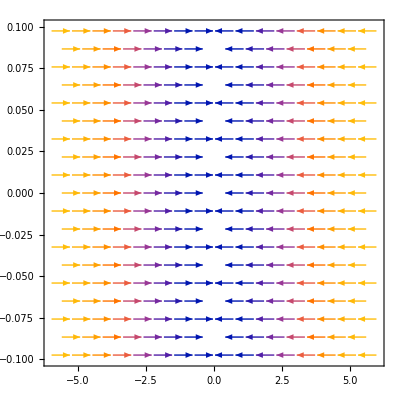

```mathematica
VectorPlot[{Sin[x]-x,0},{x,-6,6},{y,-0.1,0.1}]
```

```mathematica
(* g) f(x)=-x^(1/3) *)
```

```mathematica
x=.;
Solve[{-x^(1/3)==x},x]
```

{{x→0}}

```mathematica
x=.;
D[-x^(1/3)-x,x]
```

-1-1/(3 x^(2/3))

```mathematica
(* h) f(x)=-4/π*ArcTan[x] *)
```

```mathematica
x=.;
NSolve[{-4/π*ArcTan[x]==x},x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[{-(4 ArcTan[x])/π==x},x]

```mathematica
x=.;
D[-(4*ArcTan[x])/π-x,x]
```

-1-4/(π (1+x^2))

```mathematica
-1-4/π//N
```

-2.27324

## Problema 7.2

```mathematica
r=.;
Solve[{r*x*(1-x)==x},x]
```

{{x→0},{x→(-1+r)/r}}

```mathematica
D[r*x*(1-x),x]
```

r (1-x)-r x

## Problema 14.2

```mathematica
AbsArg[1-4*I]//N
AbsArg[1/2+3/4*I]//N
```

{4.12311,-1.32582}

{0.901388,0.982794}

## Problema 14.3

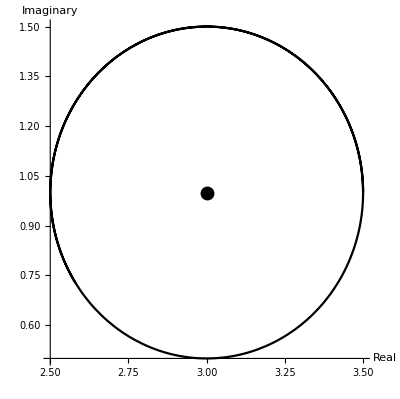

```mathematica
(* Para 3+i, radio 1/2 *)
bola1=ParametricPlot[{0.5*Cos[t]+3,0.5*Sin[t]+1},{t,0,10},PlotStyle->Black,AxesLabel->{"Real","Imaginary"}];
center1=Graphics[{PointSize[0.025],Point[{{3,1}},VertexColors->{Green}]}];

Show[bola1,center1]
```

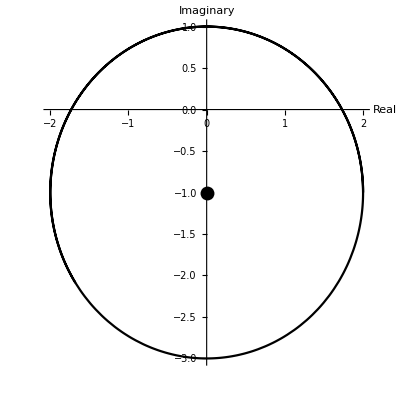

```mathematica
(* Para -i, radio 2 *)
bola2=ParametricPlot[{2*Cos[t],2*Sin[t]-1},{t,0,10},PlotStyle->Black,AxesLabel->{"Real","Imaginary"}];
center2=Graphics[{PointSize[0.025],Point[{{0,-1}},VertexColors->{Green}]}];

Show[bola2,center2]
```

## Problema 14.4

```mathematica
z=.;
Solve[{z^2==8},z]
```

{{z→-2 √2},{z→2 √2}}

```mathematica
z=.;
Solve[{z^3==8},z]
```

{{z→2},{z→-2 (-1)^(1/3)},{z→2 (-1)^(2/3)}}

```mathematica
z=.;
Solve[{z^#==1},z]&/@Range[2,6]
```

{{{z→-1},{z→1}},{{z→1},{z→-(-1)^(1/3)},{z→(-1)^(2/3)}},{{z→-1},{z→-ⅈ},{z→ⅈ},{z→1}},{{z→1},{z→-(-1)^(1/5)},{z→(-1)^(2/5)},{z→-(-1)^(3/5)},{z→(-1)^(4/5)}},{{z→-1},{z→1},{z→-(-1)^(1/3)},{z→(-1)^(1/3)},{z→-(-1)^(2/3)},{z→(-1)^(2/3)}}}

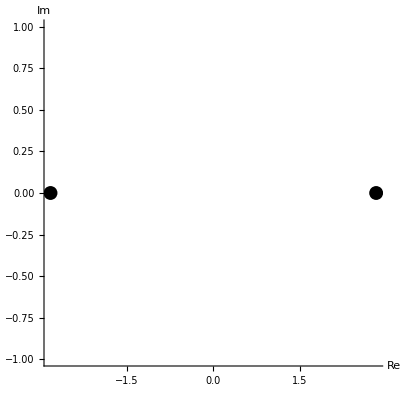

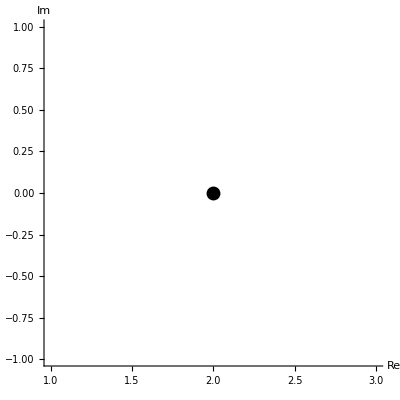

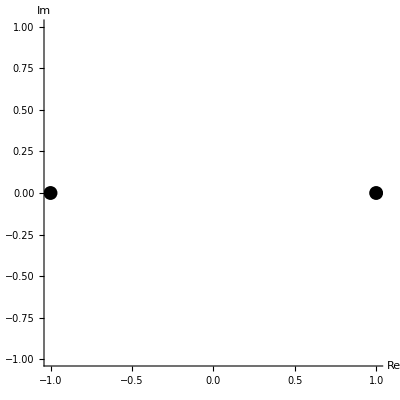

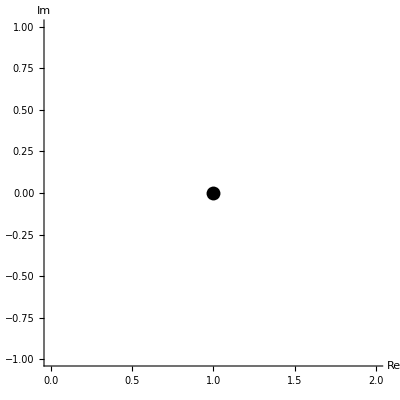

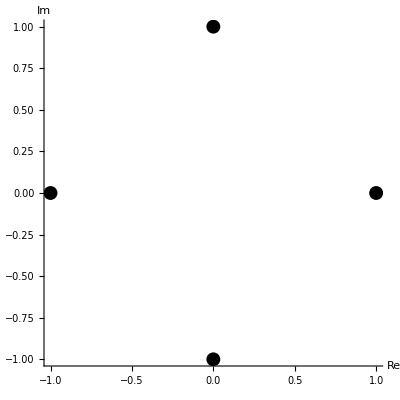

-Graphics-

-Graphics-

```mathematica
(* a) *)
Graphics[{PointSize[0.025],Point[{{-2*√2,0},{2*√2,0}},VertexColors->{Blue,Blue}]},Axes->True,AxesLabel->{"Re","Im"},AspectRatio->1]
(* b) *)
Graphics[{PointSize[0.025],Point[{{2,0}},VertexColors->{Blue}]},Axes->True,AxesLabel->{"Re","Im"},AspectRatio->1]
(* c) *)
(* 2 *)
Graphics[{PointSize[0.025],Point[{{-1,0},{1,0}},VertexColors->{Blue,Blue}]},Axes->True,AxesLabel->{"Re","Im"},AspectRatio->1]
(* 3 *)
Graphics[{PointSize[0.025],Point[{{1,0}},VertexColors->{Blue}]},Axes->True,AxesLabel->{"Re","Im"},AspectRatio->1]
(* 4 *)
Graphics[{PointSize[0.025],Point[{{-1,0},{1,0},{0,-1},{0,1}},VertexColors->{Blue,Blue,Blue,Blue}]},Axes->True,AxesLabel->{"Re","Im"},AspectRatio->1]
(* 5 *)
Graphics[{PointSize[0.025],Point[{{1,0}},VertexColors->{Blue}]},Axes->True,AxesLabel->{"Re","Im"},AspectRatio->1]
(* 6 *)
Graphics[{PointSize[0.025],Point[{{-1,0},{1,0}},VertexColors->{Blue,Blue}]},Axes->True,AxesLabel->{"Re","Im"},AspectRatio->1]
```